# B_c Mixing Angle: Momentum-Space QCD Sum Rule

This notebook is a thin wrapper around BcMixingMomentum.wl. Evaluate the cells from top to bottom in a Wolfram kernel where FeynCalc is installed.

## Load

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["BcMixingMomentum.wl"]
```

Loaded BcMixingMomentum.wl.  Run CheckEnvironment[] for setup information.

```mathematica
CheckEnvironment[]
```

<|FeynCalcLoaded→True,FeynCalcVersion→10.2.0,TensorCurrentKeepsRawI→True,TensorCurrentScale→mb+mc,Nc→3,Threshold→(mb+mc)^2,DefaultParameters→<|mb→4.18,mc→1.27,G2→0.473741,G3→0.57,alphaS→0.26,M2→10.,s0→55.|>,DefaultUncertaintyRanges→<|mb→{4.16,4.21},mc→{1.25,1.29},G2→{0.236871,0.710612},G3→{0.28,0.86},M2→{8.,12.},s0→{50.,60.}|>,MonteCarloIncludeG3→False|>

## Mass-Dimension Checks

The tensor current is normalized with p/(mb+mc), so AA, AB, BA, and BB have compatible spectral-density dimensions. The False case shows the deliberately unnormalized convention.

```mathematica
MixingMassDimensionReport[]
```

<|AA→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>,AB→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>,BA→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>,BB→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>|>

```mathematica
CheckMixingMassDimensions[]
```

True

```mathematica
PerturbativeSpectralDensityDimensionReport[]
```

<|AA→<|Name→rhoPertAA,Dimension→2,Expected→2,Pass→True|>,AB→<|Name→rhoPertAB,Dimension→2,Expected→2,Pass→True|>,BA→<|Name→rhoPertBA,Dimension→2,Expected→2,Pass→True|>,BB→<|Name→rhoPertBB,Dimension→2,Expected→2,Pass→True|>|>

```mathematica
MixingMassDimensionReport[False]
```

<|AA→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>,AB→<|CurrentDimensions→{3,4},CorrelatorDimension→3,SpectralDensityDimension→3,BorelMomentDimensionInThisConvention→5|>,BA→<|CurrentDimensions→{4,3},CorrelatorDimension→3,SpectralDensityDimension→3,BorelMomentDimensionInThisConvention→5|>,BB→<|CurrentDimensions→{4,4},CorrelatorDimension→4,SpectralDensityDimension→4,BorelMomentDimensionInThisConvention→6|>|>

```mathematica
CheckMixingMassDimensions[False]
```

False

## Projected Loop Integrands

These cells build the spin-1 projected OPE-side integrands before the final spectral-density step.

```mathematica
Correlator["AA","pert"]//Short
```

-(4 (2 (k̄·p̄)^2-3 («1»)^2 (k̄·p̄)+(3 mb mc+(k̄)^2) (p̄)^2))/((k^2-mc^2) ((k-p)^2-mb^2) (p̄)^2)

```mathematica
Correlator["AB","pert"]//Short
```

-(12 ((mb+mc) (k̄·p̄)-mc (p̄)^2))/((mb+mc) (k^2-mc^2) ((k-p)^2-mb^2))

```mathematica
Correlator["BB","pert"]//Short
```

-(4 (4 (k̄·p̄)^2-3 («1»)^2 (k̄·p̄)+(3 mb mc-(k̄)^2) (p̄)^2))/((mb+mc)^2 (k^2-mc^2) ((k-p)^2-mb^2))

```mathematica
Correlator["AA","G2"]//Short
```

-(G2 ((2 («1»)^2+«1»-5 («1»)^2 («1»)^2)/((«1»)^2 («1»)^2)+(«1»)/(«1»)+(«1»)/((«1»)«1»«1»)))/(18 (p̄)^2)

```mathematica
Correlator["AA","G3"]//Short
```

1/12 G3 (-(2 (mc^2-(k̄)^2) (k̄)^2 (7 mc^2+(k̄)^2))/((k^2-mc^2)^6 ((k-p)^2-mb^2))+(2 «3»)/(((«1»«1»)^6 («1»))+(«1»)/(«1»)+«1»+«1»+(«1»)/(«1»)-(((«1»-«1»)«1»«1»)/((«1»)^6 («1»))+«1»)/(p̄)^2)

## Feynman-Parameter Representation

Use these expressions to derive or check rho[channel, order][s]. The output is a list of {parameterIntegrand, prefactor, variables}, one item per scalar loop-integral term.

```mathematica
FeynmanParameterForm["AA","pert"]
```

((x(1)+x(2))^(2 eps-2) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^-eps | -3 ⅈ 2^(2 eps-2) π^(eps-2) mb mc eps | {x(1),x(2)}
(x(1)+x(2))^(2 eps-4) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^-eps (eps mb^2 (x(2))^2+eps mb^2 x(1) x(2)+eps mc^2 (x(1))^2+eps mc^2 x(1) x(2)+eps s (x(2))^2-eps s x(1) x(2)-2 mb^2 (x(2))^2-2 mb^2 x(1) x(2)-2 mc^2 (x(1))^2-2 mc^2 x(1) x(2)-s (x(2))^2+2 s x(1) x(2)) | -ⅈ 2^(2 eps-2) π^(eps-2) eps-1 | {x(1),x(2)}
x(2) (x(1)+x(2))^(2 eps-3) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^-eps | -3 ⅈ 2^(4 eps-2) (1/2 (4-2 eps)-1) π^(eps-2) s eps-1 | {x(1),x(2)}
(x(1)+x(2))^(2 eps-4) (8 (1/2 (4-2 eps)-1) (4-2 eps) s^2 (x(2))^2 (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^-eps+(4-2 eps) s (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(1-eps)) | -(ⅈ 2^(4 eps-5) π^(eps-2) eps-2)/s | {x(1),x(2)})

```mathematica
FeynmanParameterForm["AB","pert"]
```

((x(1)+x(2))^(2 eps-2) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^-eps | (3 ⅈ 2^(2 eps-2) π^(eps-2) mc s eps)/(mb+mc) | {x(1),x(2)}
x(2) (x(1)+x(2))^(2 eps-3) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^-eps | (3 ⅈ 2^(4 eps-2) (1/2 (4-2 eps)-1) π^(eps-2) mb s eps-1)/(mb+mc) | {x(1),x(2)}
x(2) (x(1)+x(2))^(2 eps-3) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^-eps | (3 ⅈ 2^(4 eps-2) (1/2 (4-2 eps)-1) π^(eps-2) mc s eps-1)/(mb+mc) | {x(1),x(2)})

```mathematica
FeynmanParameterForm["BB","pert"]
```

((x(1)+x(2))^(2 eps-2) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^-eps | -(3 ⅈ 2^(2 eps-2) π^(eps-2) mb mc s eps)/(mb+mc)^2 | {x(1),x(2)}
(x(1)+x(2))^(2 eps-4) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^-eps (eps mb^2 (x(2))^2+eps mb^2 x(1) x(2)+eps mc^2 (x(1))^2+eps mc^2 x(1) x(2)+eps s (x(2))^2-eps s x(1) x(2)-2 mb^2 (x(2))^2-2 mb^2 x(1) x(2)-2 mc^2 (x(1))^2-2 mc^2 x(1) x(2)-s (x(2))^2+2 s x(1) x(2)) | (ⅈ 2^(2 eps-2) π^(eps-2) s eps-1)/(mb+mc)^2 | {x(1),x(2)}
x(2) (x(1)+x(2))^(2 eps-3) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^-eps | -(3 ⅈ 2^(4 eps-2) (1/2 (4-2 eps)-1) π^(eps-2) s^2 eps-1)/(mb+mc)^2 | {x(1),x(2)}
(x(1)+x(2))^(2 eps-4) (8 (1/2 (4-2 eps)-1) (4-2 eps) s^2 (x(2))^2 (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^-eps+(4-2 eps) s (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(1-eps)) | -(ⅈ 2^(4 eps-4) π^(eps-2) eps-2)/(mb+mc)^2 | {x(1),x(2)})

```mathematica
FeynmanParameterForm["AA","G2"]
```

((x(2))^3 (x(1)+x(2))^(2 eps+1) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-3) | 1/3 ⅈ 2^(2 eps-5) π^(eps-2) G2 mb mc s eps+3 | {x(1),x(2)}
x(1) x(2) (-((1/2 (4-2 eps)-3) (x(1)+x(2))^(2 eps-1) (mb^2 x(2)+mc^2 x(1)-s x(2)) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-2))-(2 eps-1) (x(1)+x(2))^(2 eps-2) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-1)) | -5/9 ⅈ 2^(2 eps-5) π^(eps-2) G2 eps+1 | {x(1),x(2)}
(x(1))^3 (-((1/2 (4-2 eps)-4) (x(1)+x(2))^(2 eps) (mb^2 x(2)+mc^2 x(1)-s x(2)) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-3))-2 eps (x(1)+x(2))^(2 eps-1) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-2)) | -1/3 ⅈ 2^(2 eps-5) π^(eps-2) G2 mb mc eps+2 | {x(1),x(2)}
(x(1))^3 (-((1/2 (4-2 eps)-4) (x(1)+x(2))^(2 eps) (mb^2 x(2)+mc^2 x(1)-s x(2)) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-3))-2 eps (x(1)+x(2))^(2 eps-1) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-2)) | -1/9 ⅈ 2^(2 eps-5) π^(eps-2) G2 mc^2 eps+2 | {x(1),x(2)}
(x(2))^3 (-((1/2 (4-2 eps)-4) (x(1)+x(2))^(2 eps) (mb^2 x(2)+mc^2 x(1)-s x(2)) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-3))-2 eps (x(1)+x(2))^(2 eps-1) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-2)) | -1/9 ⅈ 2^(2 eps-5) π^(eps-2) G2 mb^2 eps+2 | {x(1),x(2)}
(x(2))^3 (-((1/2 (4-2 eps)-4) (x(1)+x(2))^(2 eps) (mb^2 x(2)+mc^2 x(1)-s x(2)) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-3))-2 eps (x(1)+x(2))^(2 eps-1) (mb^2 (x(2))^2+mb^2 x(1) x(2)+mc^2 (x(1))^2+mc^2 x(1) x(2)-s x(1) x(2))^(-eps-2)) | -1/3 ⅈ 2^(2 eps-5) π^(eps-2) G2 mb mc eps+2 | {x(1),x(2)}
x(1) (x(2))^2 (x(1)+x(2))^(2 eps-1) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-2) | 1/3 ⅈ 2^(4 eps-1) (1/2 (4-2 eps)-3) π^(eps-2) G2 s eps+1 | {x(1),x(2)}
(x(1))^3 x(2) (x(1)+x(2))^(2 eps) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-3) | 1/3 ⅈ 2^(4 eps+1) (1/2 (4-2 eps)-4) π^(eps-2) G2 mc^2 s eps+2 | {x(1),x(2)}
(x(2))^4 (x(1)+x(2))^(2 eps) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-3) | 1/3 ⅈ 2^(4 eps+1) (1/2 (4-2 eps)-4) π^(eps-2) G2 mb^2 s eps+2 | {x(1),x(2)}
(x(2))^4 (x(1)+x(2))^(2 eps) (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-3) | 1/3 ⅈ 2^(4 eps+2) (1/2 (4-2 eps)-4) π^(eps-2) G2 mb mc s eps+2 | {x(1),x(2)}
x(1) x(2) (x(1)+x(2))^(2 eps-2) (16 (1/2 (4-2 eps)-3) (1/2 (4-2 eps)-2) s^2 (x(2))^2 (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-2)+2 (1/2 (4-2 eps)-2) s (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-1)) | -(ⅈ 2^(4 eps-4) π^(eps-2) G2 eps)/(9 s) | {x(1),x(2)}
(x(1))^3 (x(1)+x(2))^(2 eps-1) (16 (1/2 (4-2 eps)-4) (1/2 (4-2 eps)-3) s^2 (x(2))^2 (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-3)+2 (1/2 (4-2 eps)-3) s (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-2)) | (ⅈ 2^(4 eps-2) π^(eps-2) G2 mc^2 eps+1)/(9 s) | {x(1),x(2)}
(x(2))^3 (x(1)+x(2))^(2 eps-1) (16 (1/2 (4-2 eps)-4) (1/2 (4-2 eps)-3) s^2 (x(2))^2 (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-3)+2 (1/2 (4-2 eps)-3) s (4 mb^2 (x(2))^2+4 mb^2 x(1) x(2)+4 mc^2 (x(1))^2+4 mc^2 x(1) x(2)-4 s x(1) x(2))^(-eps-2)) | (ⅈ 2^(4 eps-2) π^(eps-2) G2 mb^2 eps+1)/(9 s) | {x(1),x(2)})

```mathematica
FeynmanParameterForm["AA","G3"]
```

## Borel Moments And Mixing Angle

BorelPi is formal until spectral densities are supplied with SetSpectralDensity[channel, order, expr, s].

```mathematica
BorelPi["AA","pert"]
```

Integrate[-(3 ⅇ^(-var$4016615/M2) √(mb^4-2 mb^2 mc^2-2 mb^2 var$4016615+mc^4-2 mc^2 var$4016615+var$4016615^2) (mb^4+mb^2 (var$4016615-2 mc^2)+6 mb mc var$4016615+mc^4+mc^2 var$4016615-2 var$4016615^2))/(8 π^2 var$4016615^2),{var$4016615,(mb+mc)^2,s0},Assumptions→(mb|mc|M2|s0|s|G2|G3|alphaS)∈ℝ∧mb>0∧mc>0∧M2>0∧s0>(mb+mc)^2∧G2≥0∧G3≥0∧alphaS≥0]

```mathematica
MixingAngle[M2,s0]
```

1/2 tan^-1(Integrate[ⅇ^(-var$4040606/M2) (rho(AA,G2b)(var$4040606)+rho(AA,G2c)(var$4040606)+rho(AA,G2gg)(var$4040606)+rho(AA,G3b)(var$4040606)+rho(AA,G3c)(var$4040606)-(3 √(mb^4-2 mb^2 mc^2-2 mb^2 var$4040606+mc^4-2 mc^2 var$4040606+var$4040606^2) (mb^4+mb^2 (var$4040606-2 mc^2)+6 mb mc var$4040606+mc^4+mc^2 var$4040606-2 var$4040606^2))/(8 π^2 var$4040606^2)),{var$4040606,(mb+mc)^2,s0},Assumptions→(mb|mc|M2|s0|s|G2|G3|alphaS)∈ℝ∧mb>0∧mc>0∧M2>0∧s0>(mb+mc)^2∧G2≥0∧G3≥0∧alphaS≥0]-Integrate[ⅇ^(-var$4040617/M2) (rho(BB,G2b)(var$4040617)+rho(BB,G2c)(var$4040617)+rho(BB,G2gg)(var$4040617)+rho(BB,G3b)(var$4040617)+rho(BB,G3c)(var$4040617)+(3 √(mb^4-2 mb^2 mc^2-2 mb^2 var$4040617+mc^4-2 mc^2 var$4040617+var$4040617^2) (-2 mb^4+mb^2 (4 mc^2+var$4040617)-6 mb mc var$4040617-2 mc^4+mc^2 var$4040617+var$4040617^2))/(8 π^2 var$4040617 (mb+mc)^2)),{var$4040617,(mb+mc)^2,s0},Assumptions→(mb|mc|M2|s0|s|G2|G3|alphaS)∈ℝ∧mb>0∧mc>0∧M2>0∧s0>(mb+mc)^2∧G2≥0∧G3≥0∧alphaS≥0],-2 Integrate[ⅇ^(-var$4040628/M2) (rho(AB,G2b)(var$4040628)+rho(AB,G2c)(var$4040628)+rho(AB,G2gg)(var$4040628)+rho(AB,G3b)(var$4040628)+rho(AB,G3c)(var$4040628)+(9 (mb-mc) √(mb^4-2 mb^2 mc^2-2 mb^2 var$4040628+mc^4-2 mc^2 var$4040628+var$4040628^2) (mb^2+2 mb mc+mc^2-var$4040628))/(8 π^2 var$4040628 (mb+mc))),{var$4040628,(mb+mc)^2,s0},Assumptions→(mb|mc|M2|s0|s|G2|G3|alphaS)∈ℝ∧mb>0∧mc>0∧M2>0∧s0>(mb+mc)^2∧G2≥0∧G3≥0∧alphaS≥0])

The line above is formal unless every requested rho is installed. For numerical work, use the Numeric* functions. Perturbative rho is installed automatically; G2 and the standard single-line G3 term are evaluated as direct Borel moments.

```mathematica
NumericMixingAngleDegrees[10,55,"pert"]
```

43.7261

```mathematica
NumericMixingAngleDegrees[10,55,"pertG2"]
```

43.7474

```mathematica
NumericMixingAngleDegrees[10,55,"total"]
```

43.7427

```mathematica
NumericOPESummary[10,55]
```

<|AA→<|pert→0.144172,G2→-0.000365828,G3→0.0000700979,pertG2→0.143806,total→0.143876,G2OverPert→-0.00253744,G3OverPert→0.000486211|>,AB→<|pert→-0.105158,G2→0.000230942,G3→-0.0000493659,pertG2→-0.104927,total→-0.104976,G2OverPert→-0.00219615,G3OverPert→0.000469447|>,BB→<|pert→0.134813,G2→-0.000188887,G3→0.0000310238,pertG2→0.134625,total→0.134656,G2OverPert→-0.0014011,G3OverPert→0.000230124|>|>

```mathematica
OPESummary[M2,s0]
```

<|AA→<|pert→0.144172,G2→Integrate[2.71828^(-0.1 var$4077914) (rho(AA,G2b)(var$4077914)+rho(AA,G2c)(var$4077914)+rho(AA,G2gg)(var$4077914)),{var$4077914,29.7025,55.},Assumptions→s∈ℝ],G3→Integrate[2.71828^(-0.1 var$4077920) (rho(AA,G3b)(var$4077920)+rho(AA,G3c)(var$4077920)),{var$4077920,29.7025,55.},Assumptions→s∈ℝ],pertG2→Integrate[2.71828^(-0.1 var$4077925) (rho(AA,G2b)(var$4077925)+rho(AA,G2c)(var$4077925)+rho(AA,G2gg)(var$4077925)-(0.0379954 √(var$4077925^2-38.1706 var$4077925+251.524) (-2. var$4077925^2+33.4645 var$4077925+17.4724 (var$4077925-3.2258)+307.886))/var$4077925^2),{var$4077925,29.7025,55.},Assumptions→s∈ℝ],total→Integrate[2.71828^(-0.1 var$4077933) (rho(AA,G2b)(var$4077933)+rho(AA,G2c)(var$4077933)+rho(AA,G2gg)(var$4077933)+rho(AA,G3b)(var$4077933)+rho(AA,G3c)(var$4077933)-(0.0379954 √(var$4077933^2-38.1706 var$4077933+251.524) (-2. var$4077933^2+33.4645 var$4077933+17.4724 (var$4077933-3.2258)+307.886))/var$4077933^2),{var$4077933,29.7025,55.},Assumptions→s∈ℝ],G2OverPert→6.93617 Integrate[2.71828^(-0.1 var$4077945) (rho(AA,G2b)(var$4077945)+rho(AA,G2c)(var$4077945)+rho(AA,G2gg)(var$4077945)),{var$4077945,29.7025,55.},Assumptions→s∈ℝ],G3OverPert→6.93617 Integrate[2.71828^(-0.1 var$4107792) (rho(AA,G3b)(var$4107792)+rho(AA,G3c)(var$4107792)),{var$4107792,29.7025,55.},Assumptions→s∈ℝ]|>,AB→<|pert→-0.105158,G2→Integrate[2.71828^(-0.1 var$4162435) (rho(AB,G2b)(var$4162435)+rho(AB,G2c)(var$4162435)+rho(AB,G2gg)(var$4162435)),{var$4162435,29.7025,55.},Assumptions→s∈ℝ],G3→Integrate[2.71828^(-0.1 var$4162441) (rho(AB,G3b)(var$4162441)+rho(AB,G3c)(var$4162441)),{var$4162441,29.7025,55.},Assumptions→s∈ℝ],pertG2→Integrate[2.71828^(-0.1 var$4162446) (rho(AB,G2b)(var$4162446)+rho(AB,G2c)(var$4162446)+rho(AB,G2gg)(var$4162446)+(0.0608624 √(var$4162446^2-38.1706 var$4162446+251.524) (29.7025-1. var$4162446))/var$4162446),{var$4162446,29.7025,55.},Assumptions→s∈ℝ],total→Integrate[2.71828^(-0.1 var$4162454) (rho(AB,G2b)(var$4162454)+rho(AB,G2c)(var$4162454)+rho(AB,G2gg)(var$4162454)+rho(AB,G3b)(var$4162454)+rho(AB,G3c)(var$4162454)+(0.0608624 √(var$4162454^2-38.1706 var$4162454+251.524) (29.7025-1. var$4162454))/var$4162454),{var$4162454,29.7025,55.},Assumptions→s∈ℝ],G2OverPert→-9.50953 Integrate[2.71828^(-0.1 var$4162466) (rho(AB,G2b)(var$4162466)+rho(AB,G2c)(var$4162466)+rho(AB,G2gg)(var$4162466)),{var$4162466,29.7025,55.},Assumptions→s∈ℝ],G3OverPert→-9.50953 Integrate[2.71828^(-0.1 var$4187381) (rho(AB,G3b)(var$4187381)+rho(AB,G3c)(var$4187381)),{var$4187381,29.7025,55.},Assumptions→s∈ℝ]|>,BB→<|pert→0.134813,G2→Integrate[2.71828^(-0.1 var$4240567) (rho(BB,G2b)(var$4240567)+rho(BB,G2c)(var$4240567)+rho(BB,G2gg)(var$4240567)),{var$4240567,29.7025,55.},Assumptions→s∈ℝ],G3→Integrate[2.71828^(-0.1 var$4240573) (rho(BB,G3b)(var$4240573)+rho(BB,G3c)(var$4240573)),{var$4240573,29.7025,55.},Assumptions→s∈ℝ],pertG2→Integrate[2.71828^(-0.1 var$4240578) (rho(BB,G2b)(var$4240578)+rho(BB,G2c)(var$4240578)+rho(BB,G2gg)(var$4240578)+(0.0012792 √(var$4240578^2-38.1706 var$4240578+251.524) (var$4240578^2-30.2387 var$4240578+17.4724 (var$4240578+6.4516)-615.772))/var$4240578),{var$4240578,29.7025,55.},Assumptions→s∈ℝ],total→Integrate[2.71828^(-0.1 var$4240586) (rho(BB,G2b)(var$4240586)+rho(BB,G2c)(var$4240586)+rho(BB,G2gg)(var$4240586)+rho(BB,G3b)(var$4240586)+rho(BB,G3c)(var$4240586)+(0.0012792 √(var$4240586^2-38.1706 var$4240586+251.524) (var$4240586^2-30.2387 var$4240586+17.4724 (var$4240586+6.4516)-615.772))/var$4240586),{var$4240586,29.7025,55.},Assumptions→s∈ℝ],G2OverPert→7.41766 Integrate[2.71828^(-0.1 var$4240598) (rho(BB,G2b)(var$4240598)+rho(BB,G2c)(var$4240598)+rho(BB,G2gg)(var$4240598)),{var$4240598,29.7025,55.},Assumptions→s∈ℝ],G3OverPert→7.41766 Integrate[2.71828^(-0.1 var$4269121) (rho(BB,G3b)(var$4269121)+rho(BB,G3c)(var$4269121)),{var$4269121,29.7025,55.},Assumptions→s∈ℝ]|>|>

## Alpha_s K-Factor Sensitivity

This is not a full NLO calculation. It rescales only the perturbative moment by 1 + alphaS K_ij/Pi and leaves G2/G3 unchanged.

```mathematica
KFactorSensitivityRecord[10,55,KFactorAssociation[1,0,-1],0.26,"total"]
```

<|M2→10.,s0→55.,Order→total,alphaS→0.26,KAA→1,KAB→0,KBB→-1,MultiplierAA→1.08276,MultiplierAB→1.,MultiplierBB→0.917239,PiAAAlphaS→0.155808,PiABAlphaS→-0.104976,PiBBAlphaS→0.123498,ThetaBaseDeg→43.7427,ThetaAlphaSDeg→40.6257,DeltaThetaDeg→-3.11697|>

```mathematica
KFactorSensitivityEnvelope[10,55,{-2,2,2},0.26,"total"]
```

<|ThetaBaseDeg→43.7427,ThetaMinDeg→-43.4689,ThetaMaxDeg→44.1024,DeltaThetaMinDeg→-7.51897,DeltaThetaMaxDeg→7.21508,MaxAbsDeltaThetaDeg→7.51897,RecordAtMinTheta→<|M2→10.,s0→55.,Order→total,alphaS→0.26,KAA→0.,KAB→2.,KBB→2.,MultiplierAA→1.,MultiplierAB→1.16552,MultiplierBB→1.16552,PiAAAlphaS→0.143876,PiABAlphaS→-0.122382,PiBBAlphaS→0.15697,ThetaBaseDeg→43.7427,ThetaAlphaSDeg→-43.4689,DeltaThetaDeg→2.78842|>,RecordAtMaxTheta→<|M2→10.,s0→55.,Order→total,alphaS→0.26,KAA→-2.,KAB→2.,KBB→-2.,MultiplierAA→0.834479,MultiplierAB→1.16552,MultiplierBB→0.834479,PiAAAlphaS→0.120012,PiABAlphaS→-0.122382,PiBBAlphaS→0.112341,ThetaBaseDeg→43.7427,ThetaAlphaSDeg→44.1024,DeltaThetaDeg→0.35972|>,RecordAtMaxAbsDelta→<|M2→10.,s0→55.,Order→total,alphaS→0.26,KAA→2.,KAB→-2.,KBB→-2.,MultiplierAA→1.16552,MultiplierAB→0.834479,MultiplierBB→0.834479,PiAAAlphaS→0.167739,PiABAlphaS→-0.0875703,PiBBAlphaS→0.112341,ThetaBaseDeg→43.7427,ThetaAlphaSDeg→36.2237,DeltaThetaDeg→-7.51897|>|>

## Borel Window And s0 Scans

Use {min,max,step} specifications to scan trial Borel windows and continuum thresholds.

```mathematica
MixingAngleDataset[{8,12,1},{50,60,5},"total"]
```

```mathematica
MixingAngleTable[{8,12,1},{50,60,5},"total"]
```

M2 \ s0 | 50. | 55. | 60.
8. | 42.8331 | 43.4516 | 43.9425
9. | 42.9244 | 43.6096 | 44.1743
10. | 43.0043 | 43.7427 | 44.3683
11. | 43.0721 | 43.8538 | 44.5301
12. | 43.1294 | 43.9469 | 44.6659

```mathematica
OPEConvergenceDataset[{8,12,1},{50,60,5}]
```

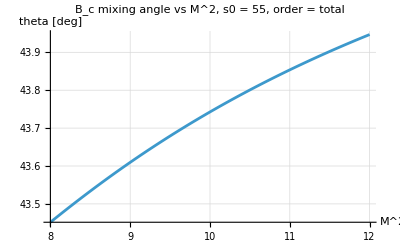

```mathematica
PlotMixingAngle[{8,12},55,$BcMixingDefaultParameters,"total"]
```

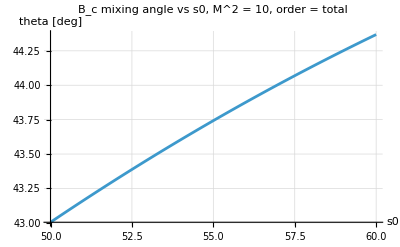

```mathematica
PlotMixingAngleS0[10,{50,60},$BcMixingDefaultParameters,"total"]
```

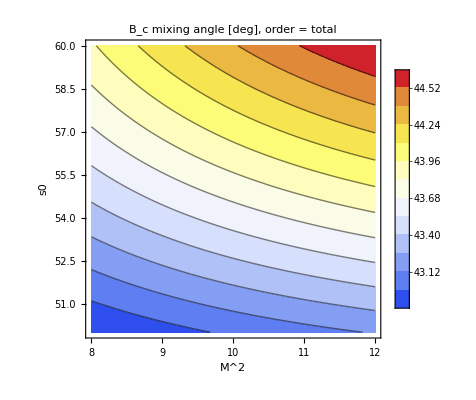

```mathematica
MixingAngleContourPlot[{8,12},{50,60},$BcMixingDefaultParameters,"total"]
```

## Wang Window Stability Plots

Publication-quality stability plots using the Wang vector Bc* auxiliary window: M2 from 7 to 9 GeV^2 and s0 = 54 +/- 1 GeV^2. The y-axis is padded to avoid visually exaggerating small changes.

```mathematica
$BcMixingWangWindow
```

<|M2Range→{7.,9.},M2Values→{7.,8.,9.},s0Central→54.,s0Range→{53.,55.},s0Values→{53.,54.,55.}|>

```mathematica
stabilityOrder = "pertG2";
```

```mathematica
m2Stability = MixingAngleStabilityM2PublicationPlot[$BcMixingWangWindow["M2Range"], $BcMixingWangWindow["s0Values"], stabilityOrder, $BcMixingDefaultParameters, "NPoints" -> 25, "YHalfWidth" -> 1.0];
```

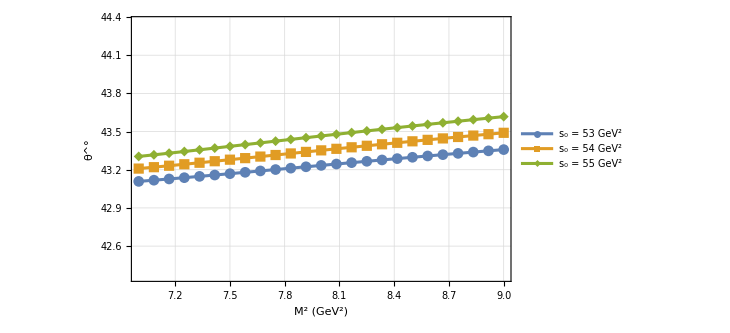

```mathematica
m2Stability["Plot"]
```

```mathematica
s0Stability = MixingAngleStabilityS0PublicationPlot[$BcMixingWangWindow["s0Range"], $BcMixingWangWindow["M2Values"], stabilityOrder, $BcMixingDefaultParameters, "NPoints" -> 25, "YHalfWidth" -> 1.0];
```

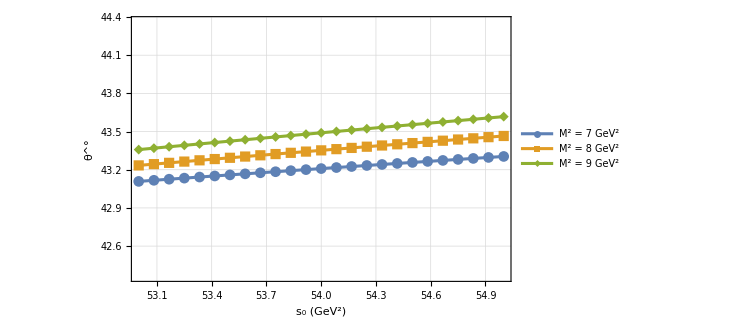

```mathematica
s0Stability["Plot"]
```

```mathematica
Export["BcMixingThetaVsM2_WangWindow.pdf", m2Stability["Plot"]]
```

BcMixingThetaVsM2_WangWindow.pdf

```mathematica
Export["BcMixingThetaVsS0_WangWindow.pdf", s0Stability["Plot"]]
```

BcMixingThetaVsS0_WangWindow.pdf

```mathematica
ExportStabilityDataCSV[m2Stability["Data"], "BcMixingThetaVsM2_WangWindow.csv", "M2"]
```

BcMixingThetaVsM2_WangWindow.csv

```mathematica
ExportStabilityDataCSV[s0Stability["Data"], "BcMixingThetaVsS0_WangWindow.csv", "s0"]
```

BcMixingThetaVsS0_WangWindow.csv

## Monte Carlo Uncertainty

The default ranges sample mb, mc, G2, G3, M2, and s0. Replace any {min,max} pair with a single number to hold that parameter fixed. The fast default keeps G3 out of the Monte Carlo scan; switch IncludeG3 to True later if needed.

Edit this control block for uncertainty studies. nSamples is the number of accepted random points, histBins is the histogram bin count, and Seed fixes the random-number sequence so the same cell is reproducible. The result is called uncertaintyRun to avoid confusion with the charm-quark mass mc.

```mathematica
$BcMixingDefaultUncertaintyRanges
```

<|mb→{4.16,4.21},mc→{1.25,1.29},G2→{0.236871,0.710612},G3→{0.28,0.86},M2→{8.,12.},s0→{50.,60.}|>

```mathematica
nSamples = 1000;
```

```mathematica
histBins = 25;
```

```mathematica
m2Range = {7.0, 9.0};
```

```mathematica
s0Range = {53.0, 55.0};
```

```mathematica
uncertaintyRanges = Join[$BcMixingDefaultUncertaintyRanges, <|"M2" -> m2Range, "s0" -> s0Range|>];
```

```mathematica
uncertaintyRun = MonteCarloMixingAngleUncertainty[nSamples, uncertaintyRanges, "total", "IncludeG3" -> True, "Seed" -> 1234, "Progress" -> True];
```

Monte Carlo sample 100/1000

Monte Carlo sample 200/1000

Monte Carlo sample 300/1000

Monte Carlo sample 400/1000

Monte Carlo sample 500/1000

Monte Carlo sample 600/1000

Monte Carlo sample 700/1000

Monte Carlo sample 800/1000

Monte Carlo sample 900/1000

Monte Carlo sample 1000/1000

```mathematica
(*Set "IncludeG3"->True in the cell above to rerun the long scan with G3.*)
```

```mathematica
uncertaintyRun["Summary"]
```

<|Count→1000,MeanDeg→43.3013,GaussianSigmaDeg→0.151565,SampleSigmaDeg→0.15164,MedianDeg→43.3072,Quantile16Deg→43.1426,Quantile84Deg→43.4599,MinDeg→42.8919,MaxDeg→43.6765,GaussianFit→NormalDistribution[43.3013,0.151565]|>

```mathematica
MonteCarloMixingAngleDataset[uncertaintyRun]
```

Dataset[<>]

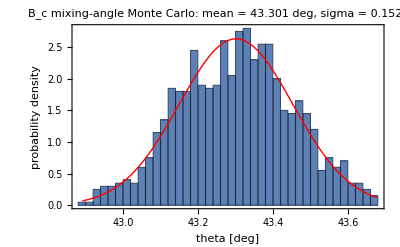

```mathematica
MonteCarloMixingAngleHistogram[uncertaintyRun,histBins]
```

```mathematica
pubPlot=MonteCarloMixingAnglePublicationHistogram[uncertaintyRun,histBins];
```

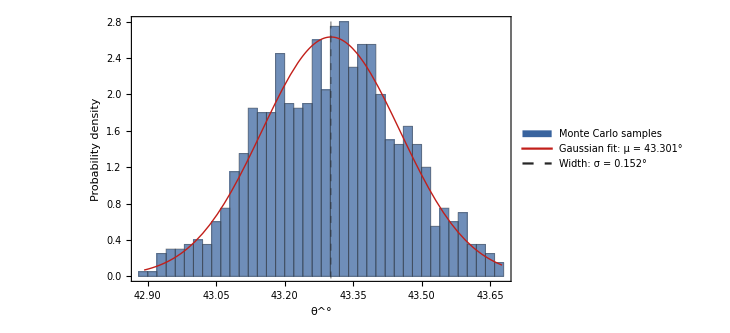

```mathematica
pubPlot
```

```mathematica
Export["BcMixingMonteCarloHistogram.pdf",pubPlot]
```

BcMixingMonteCarloHistogram.pdf

```mathematica
ExportMonteCarloMixingAngleSamples[uncertaintyRun,"BcMixingMonteCarloSamples.csv"]
```

BcMixingMonteCarloSamples.csv

```mathematica
ExportMonteCarloMixingAngleSummary[uncertaintyRun,"BcMixingMonteCarloSummary.csv"]
```

BcMixingMonteCarloSummary.csv

## Optional Manual Override

The current workflow installs perturbative rho automatically and evaluates G2/G3 as direct Borel moments. Use SetSpectralDensity only if you want to override a built-in perturbative spectral density for an independent cross-check.

```mathematica
(*SetSpectralDensity["AA","pert",rhoAApertIndependent[s],s];*)
```

## G3 Caveat

The implemented G3 term is the standard vacuum-averaged single-line contribution S_c^(G3) S_b^0 + S_c^0 S_b^(G3). Cross-line open-field G3 terms require a separate derivation and are not guessed in this file.